```mathematica
lst = {1, 2, 3, "Mathematica"}
```

{1,2,3,Mathematica}

```mathematica
lst⟦4⟧
```

Mathematica

```mathematica
lst[[{1,3}]]
```

{1,3}

```mathematica
d = {{2,6,10},{4,8,12},{6,10,14},{8,12,16},{10,14,18}}
```

{{2,6,10},{4,8,12},{6,10,14},{8,12,16},{10,14,18}}

```mathematica
d[[1, {1,2}]]
```

{2,6}

```mathematica
d[[All,3]]
```

{10,12,14,16,18}

```mathematica
d[[;;,3]]
```

{10,12,14,16,18}

```mathematica
d[[2;;4,1]]
```

{4,6,8}

```mathematica
data ={15.4,12.3,16.3,15.0,20.1,19,8,15.2,16.5,15.0,18.3,14.3,9.8,2.1,18.3,17.2,15.5,25.9,14.9,20.1}
```

{15.4,12.3,16.3,15.,20.1,19,8,15.2,16.5,15.,18.3,14.3,9.8,2.1,18.3,17.2,15.5,25.9,14.9,20.1}

```mathematica
Select[data, #>=18&]
```

{20.1,19,18.3,18.3,25.9,20.1}

```mathematica
subjectOne=Association["weight"->200,"height"->72,"age"->33]
subjectTwo=Association["weight"->180,"height"->80,"age"->34]
subjectThree=Association["weight"->170,"height"->70,"age"->53]
subjectFour=Association["weight"->180,"height"->72,"age"->22]
subjectFive=Association["weight"->150,"height"->55,"age"->61]
```

<|weight→200,height→72,age→33|>

<|weight→180,height→80,age→34|>

<|weight→170,height→70,age→53|>

<|weight→180,height→72,age→22|>

<|weight→150,height→55,age→61|>

```mathematica
dataset=Dataset[{subjectOne,subjectTwo,subjectThree,subjectFour,subjectFive}]
```

```mathematica
Take[dataset, 2]
```

```mathematica
dataset[[1]]
```

```mathematica
dataset[[1,1;;2]]
```

```mathematica
Normal[dataset[[All,1]]]
```

```mathematica
{200,180,170,180,150}
```

```mathematica
dataset[Select[#weight>170&]]
```

```mathematica
dataset[Select[#height==72&],{"weight","age"}]
```

```mathematica
dataset[Mean, "weight"]//N
```

176.

```mathematica
dataset[[All,"weight"]]
```

```mathematica
dataset[List,"weight"]
```

```mathematica
Length[dataset]
```

5

```mathematica
Dimensions[dataset]
```

{5,3}

```mathematica
subjects=Dataset[{
<|"a"->1,"b"->"x","c"->1|>,
<|"a"->2,"b"->"y","c"->2|>,
<|"a"->3,"b"->"z","c"->2|>,
<|"a"->4,"b"->"x","c"->3|>,
<|"a"->5,"b"->"y","c"->5|>,
<|"a"->6,"b"->"z","c"->3|>}]
```

```mathematica
subjects[GroupBy["b"], Mean, "c"]
```

```mathematica
SetDirectory["~/Documents/misc/mathematica/Klopper-Notebooks"]
```

/Users/chl/Documents/misc/mathematica/Klopper-Notebooks

```mathematica
data=SemanticImport["Variables.csv"]
```

```mathematica
data[[;;5]]
```

```mathematica
data[Counts, "Logistics"]
```

```mathematica
data[GroupBy["TreatmentGroup"],Counts, "Logistics"]
```

```mathematica
data[{Min,Max},"Age"]
```

```mathematica
SeedRandom[101]
age=RandomInteger[{18,80}, 50]
```

RandomGeneratorState[…]

{40,44,59,73,49,28,38,46,37,70,48,58,64,19,78,55,78,23,53,72,32,42,33,79,18,76,29,74,23,63,80,61,58,30,55,23,57,18,78,37,21,73,35,79,30,55,19,46,65,78}

```mathematica
Max[Counts[data[[All,"Logistics"]]]]
```

362

```mathematica
Sort[Counts[data[[All,"Logistics"]]], Greater]
```

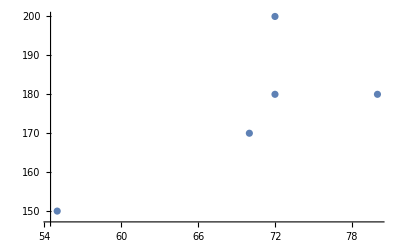

```mathematica
dataset[ListPlot, {"height", "weight"}]
```

```mathematica
data[GroupBy["InsulinDependentDiabetic"], Mean, "HB"]
```

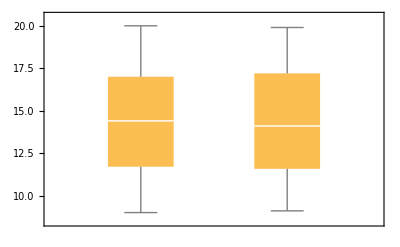

```mathematica
BoxWhiskerChart[Normal[data[GroupBy["InsulinDependentDiabetic"], All, "HB"]]]
```

```mathematica
data[GroupBy["InsulinDependentDiabetic"], {Min, Quartiles, Max}, "HB"]
```

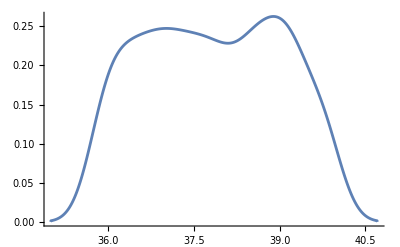

```mathematica
data[SmoothHistogram, "Temp"]
```

```mathematica
PDF[DiscreteUniformDistribution[{1,6}],3]
```

1/6

```mathematica
Probability[x==3, x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/6

```mathematica
PDF[DiscreteUniformDistribution[{a,b}],k]
```

Piecewise[{{1/(1-a+b), a≤k≤b}, {0, True}}]

```mathematica
∫Piecewise[{{1/(1-a+b),a≤k≤b}},0]ⅆa
```

Piecewise[{{-Log[1-a+b], a-k≤0&&b-k≥0}, {0, True}}]

```mathematica
dice=RandomVariate[DiscreteUniformDistribution[{1,6}],{10000,2}];
```

```mathematica
dice[[;;5]]
```

{{4,6},{4,4},{2,2},{6,6},{2,1}}

```mathematica
Head[dice]
```

List

```mathematica
totals=Plus@@@dice;
totals[[;;5]]
```

{10,8,4,12,3}

```mathematica
counts = SortBy[Tally[totals], First]
```

{{2,287},{3,552},{4,856},{5,1053},{6,1414},{7,1699},{8,1366},{9,1061},{10,846},{11,605},{12,261}}

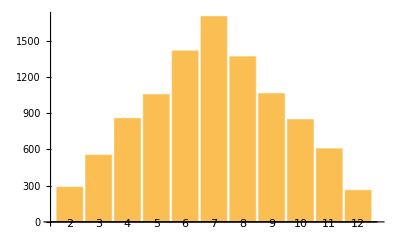

```mathematica
BarChart[counts[[All,2]], ChartLabels->counts[[All, 1]]]
```

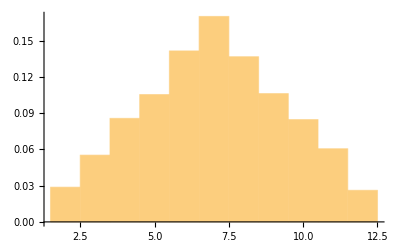

```mathematica
Histogram[totals, Automatic, "Probability"]
```

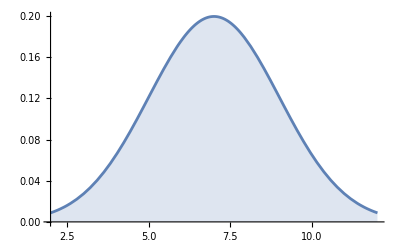

```mathematica
Plot[PDF[NormalDistribution[7, 2],x],{x,2,12},Filling->Axis]
```

```mathematica
sample=RandomVariate[NormalDistribution[7,2],60];
Mean[sample]
```

6.92931

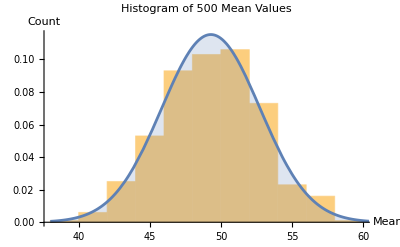

```mathematica
values=RandomVariate[DiscreteUniformDistribution[{18,80}],20000];
stats=List[];
Do[AppendTo[stats,Mean[RandomChoice[values,30]]],500];
Show[Histogram[stats,Automatic,PDF,PlotLabel->"Histogram of 500 Mean Values",AxesLabel->{"Mean","Count"}],Plot[PDF[NormalDistribution[Mean[stats],StandardDeviation[stats]],x],{x, 38,70},Filling->Axis,PlotRange->All]]
```

```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
MeanCI[stats]
```

{48.9894,49.5976}

```mathematica
1-CDF[NormalDistribution[],1.96]
```

0.0249979

```mathematica
ResourceFunction["RecordsSummary"][data[[All, {"TreatmentGroup","Age"}]]]
```

{1 TreatmentGroup
II | 299
I | 206
III | 92,2 Age
Min | 18
1st Qu | 35
Mean | 55.1039
Median | 56
3rd Qu | 75
Max | 90}

```mathematica
mass={107.6,95.6,94.3,92.3,90.7,89.4,88.8,86.9,85.8,85.5,84.4,84.1,82.5,81.4,80.8,80.8,79.,79.5,78.4,78.4,78.2,78.1,78.4,77.4,76.5,75.4,74.8,74.1,73.5,73.2,73.,72.3,72.3,72.2,71.8,71.7,71.6,71.6,71.5,71.3,70.7,70.6,70.5,69.2,68.6,68.3,117.5,67.,66.8,66.1,65.8,65.6,64.9,64.6,124.5,64.5,64.3,64.2,63.9,63.7,39.7,62.3,62.2,29.4,57.8,57.8,57.6,56.4,53.6,53.2};
```

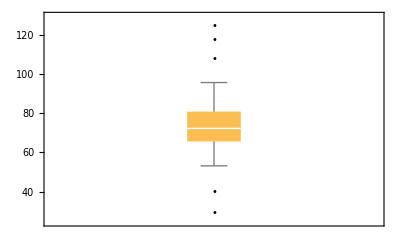

```mathematica
BoxWhiskerChart[mass,"Outliers"]
```

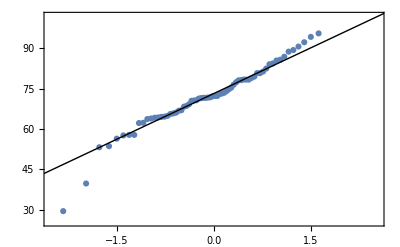

```mathematica
QuantilePlot[mass,NormalDistribution[]]
```

```mathematica
ShapiroWilkTest[mass,"TestDataTable"]
```

| Statistic | P-Value
Shapiro-Wilk | 0.938213 | 0.00183675

```mathematica
Sort[Abs[Standardize[mass]],Greater]
```

{3.41991,3.0138,2.94634,2.31699,2.27659,1.46476,1.40368,1.37682,1.37662,1.24151,1.1872,1.13327,1.10601,1.09248,1.09248,1.04532,1.00473,0.876191,0.801773,0.794815,0.78805,0.781478,0.707061,0.693337,0.686765,0.679806,0.659511,0.652746,0.639215,0.63245,0.612154,0.578522,0.564798,0.551268,0.530972,0.504104,0.483616,0.470085,0.463513,0.463513,0.382137,0.375566,0.361842,0.34174,0.321251,0.301148,0.301148,0.301148,0.287618,0.280853,0.233496,0.233303,0.226538,0.219773,0.179181,0.172609,0.165651,0.158886,0.158886,0.15212,0.145355,0.118294,0.111529,0.111529,0.0981921,0.0641728,0.0576009,0.0506424,0.0303468,0.0102445}

```mathematica
Select[Standardize[mass],#>3||#<-3&]
```

{3.41991,-3.0138}

```mathematica
LocationTest[mass, 0, {"TestDataTable","T"}]
```

LocationTest::nortst: At least one of the p-values in {0.00612265}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

| Statistic | P-Value
T | 41.8562 | 8.89554×10^-51

```mathematica
𝒦=TTest[mass, Automatic, "HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
𝒦["TestConclusion"]
```

TTest::nortst: At least one of the p-values in {0.00612265}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

The null hypothesis that the mean of the population is equal to 0 is rejected at the 5 percent level based on the T test.